# Project Cluster

```mathematica
Share[]
```

2947752

## Input Visualization

```mathematica
SetDirectory[
"C:\\Users\\hilma\\Documents\\Post Project\\MSTM\\MSTM-main\\pre"]
```

C:\Users\hilma\Documents\Post Project\MSTM\MSTM-main\pre

```mathematica
config[file_]:=Module[{f,dat,tpos,trad,p},
f=OpenRead[file];
dat=ReadList[f, Table[Number, {4}]];
tpos=Table[dat[[i,{1,2,3}]],{i,Length[dat]}];
trad=Table[dat[[i,4]],{i,Length[dat]}];
p=Table[Sphere[tpos[[i]],trad[[i]]],{i,Length[dat]}];
p];
```

## Linear chain

```mathematica
figLC10=Graphics3D[config["linear_chain_10_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["linear_chain_10_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{25*Cos@t,25*Sin@t,10},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

```mathematica
figLC20=Graphics3D[config["linear_chain_20_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["linear_chain_20_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{30*Cos@t,30*Sin@t,0},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

```mathematica
figLC30=Graphics3D[config["linear_chain_30_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["linear_chain_30_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{50*Cos@t,50*Sin@t,0},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

## Packed cluster

```mathematica
figPC10=Graphics3D[config["packed_cluster_10_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["packed_cluster_10_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{25*Cos@t,25*Sin@t,10},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

```mathematica
figPC20=Graphics3D[config["packed_cluster_20_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["packed_cluster_20_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{30*Cos@t,30*Sin@t,10},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

```mathematica
figPC30=Graphics3D[config["packed_cluster_30_config.pos"],Axes->True]
```

-Graphics3D-

```mathematica
Animate[Graphics3D[config["packed_cluster_30_config.pos"],SphericalRegion->True,ViewVector->Dynamic[{{35*Cos@t,35*Sin@t,10},{0,0,0}},None],ViewVertical->{0,0,1},ViewAngle->Automatic],{t,0,2 Pi,.1},SaveDefinitions->True]
```

## Output Visualization

```mathematica
SetDirectory[
"C:\\Users\\hilma\\Documents\\Post Project\\MSTM\\MSTM-main\\post"]
```

C:\Users\hilma\Documents\Post Project\MSTM\MSTM-main\post

```mathematica
nfread[file_]:=Module[{f,dat,sdat,pos,n,c,cdim,tdat,gmin,gmax,nb,bdat},f=OpenRead[file];
tdat={};
Do[
pos=Find[f," run number"];
If[ToString[pos]=="EndOfFile",Break[]];
n=Read[f,Number];
n=Read[f,Number];
If[n>0,c=ReadList[f,Table[Number,{4}],n],c={}];
sdat={n,c};
n=Read[f,Number];
If[n>0,c=ReadList[f,Number,n],c={}];
bdat={n,c};
gmin=Read[f,Table[Number,{3}]];
gmax=Read[f,Table[Number,{3}]];
cdim=Read[f,Table[Number,{3}]];
n=cdim[[1]]cdim[[2]]cdim[[3]];
dat=ReadList[f,Table[Number,{27}],n];
tdat=Append[tdat,{cdim,{gmin,gmax},sdat,bdat,dat}];
,{i,1,1000}];
Close[f];
tdat]
cplot[tdat_]:=Module[{cdim,rmin,rmax,splot,nb,bplot,ep,b,arat},
cdim=tdat[[1]];
p=Which[cdim[[1]]==1,1,cdim[[2]]==1,2,cdim[[3]]==1,3];
rmin=Drop[tdat[[2,1]],{p}];rmax=Drop[tdat[[2,2]],{p}];
ppos=tdat[[2,1,p]];
ns=tdat[[3,1]];sdat=tdat[[3,2]];
nis=0;ispos={};israd={};
Do[
t1=Abs[sdat[[i,p]]-ppos];
If[t1<sdat[[i,4]],
nis=nis+1;
ispos=Append[ispos,Drop[sdat[[i,{1,2,3}]],{p}]];
israd=Append[israd,Sqrt[sdat[[i,4]]^2-t1^2]];
];
,
{i,1,ns}];
splot=Table[Circle[ispos[[i]],israd[[i]]],{i,1,nis}];
nb=tdat[[4 ,1]];b=tdat[[4,2]];
bplot=If[nb>0,Table[Line[{{rmin[[1]],b[[i]]},{rmax[[1]],b[[i]]}}],{i,1,nb}],{}];
ep=Epilog->{splot,bplot};
arat=AspectRatio->Which[p==1,cdim[[3]]/cdim[[2]],p==2,cdim[[3]]/cdim[[1]],p==3,cdim[[2]]/cdim[[1]]];
{ep,arat}]
readmstm[file_,vars_,len_]:=Module[{f,newlist,str,dat,pos,tdat,t1},
f=OpenRead[file];
newlist=" input variables";
str=Find[f,newlist];
dat={};
Do[
pos=StreamPosition[f];
tdat=Table[Null[],{Length[vars]}];
Do[
str=ToString[Find[f,{newlist,vars[[j]]}]];
If[str==ToString[EndOfFile],Break[]];
If[Length[StringCases[str,vars[[j]]]]!=0,
t1=Read[f,Table[Number,{len[[j]]}]][[len[[j]]]];
tdat[[j]]=t1;
];
SetStreamPosition[f,pos];
,{j,1,Length[vars]}];
dat=Append[dat,tdat];
str=ToString[Find[f,newlist]];
If[str==ToString[EndOfFile],Break[]];
,{i,1,100000}];
Close[f];
dat]
readsmt[file_,sme_]:=Module[{f,tn,datsm,sm},
f=OpenRead[file];
Find[f,"number directions, number"];
tn=Read[f,Table[Number,{2}]];
Find[f,"  theta     11"];
datsm=ReadList[f, Table[Number, {tn[[2]]+1}],tn[[1]]];
sm=Table[datsm[[i,{1,sme}]],{i,Length[datsm]}];
Close[f];
sm]
calcsmr[sm1_,sm2_,val_]:=Module[{sm},
sm=RandomInteger[1,{Length[sm1],2}];
sm[[All,1]]=sm1[[All,1]];
sm[[All,2]]=sm2[[All,2]]/sm1[[All,2]];
If[val==1,
sm[[All,2]]=-sm[[All,2]]];
sm]
readap[file_]:=Module[{f,newlist,str,alpha11,tap,ap},
f=OpenRead[file];
newlist="    n       11          12";
ap={};
Do[str=ToString[Find[f,newlist]];
If[str==ToString[EndOfFile],Break[]];
ReadLine[f];
alpha11=Read[f,Table[Number,{2}]][[2]];
tap=alpha11/3;
ap=Append[ap,tap];,100000];
Close[f];
ap]
```

## Phase function

```mathematica
smRS1=readsmt["ref_sphere.dat",2];
smRS2=readsmt["ref_bisphere.dat",2];
smLC10=readsmt["linear_chain_10.dat",2];
smLC20=readsmt["linear_chain_20.dat",2];
smLC30=readsmt["linear_chain_30.dat",2];
smPC10=readsmt["packed_cluster_10.dat",2];
smPC20=readsmt["packed_cluster_20.dat",2];
smPC30=readsmt["packed_cluster_30.dat",2];
```

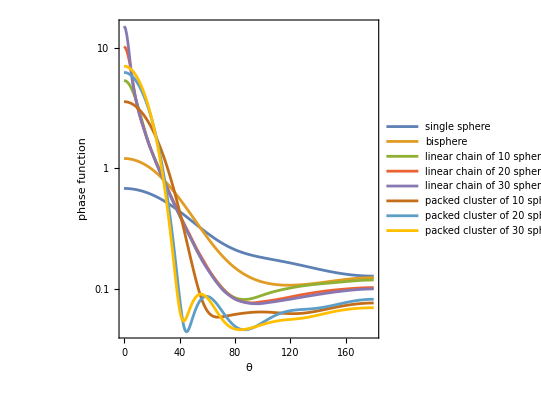

```mathematica
g=ListLogPlot[{smRS1,smRS2,smLC10,smLC20,smLC30,smPC10,smPC20,smPC30},PlotLegends->{"single sphere","bisphere","linear chain of 10 spheres","linear chain of 20 spheres","linear chain of 30 spheres","packed cluster of 10 spheres","packed cluster of 20 spheres","packed cluster of 30 spheres"}, Frame->True,Axes->True,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"θ","phase function"},PlotRangePadding->None]
```

## Linear polarization degree

```mathematica
smRS1=calcsmr[readsmt["ref_sphere.dat",2],readsmt["ref_sphere.dat",3],1];
smRS2=calcsmr[readsmt["ref_bisphere.dat",2],readsmt["ref_bisphere.dat",3],1];
smLC10=calcsmr[readsmt["linear_chain_10.dat",2],readsmt["linear_chain_10.dat",3],1];
smLC20=calcsmr[readsmt["linear_chain_20.dat",2],readsmt["linear_chain_20.dat",3],1];
smLC30=calcsmr[readsmt["linear_chain_30.dat",2],readsmt["linear_chain_30.dat",3],1];
smPC10=calcsmr[readsmt["packed_cluster_10.dat",2],readsmt["packed_cluster_10.dat",3],1];
smPC20=calcsmr[readsmt["packed_cluster_20.dat",2],readsmt["packed_cluster_20.dat",3],1];
smPC30=calcsmr[readsmt["packed_cluster_30.dat",2],readsmt["packed_cluster_30.dat",3],1];
```

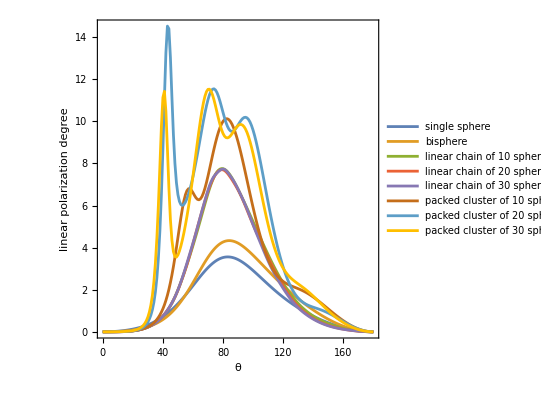

```mathematica
g=ListPlot[{smRS1,smRS2,smLC10,smLC20,smLC30,smPC10,smPC20,smPC30},PlotLegends->{"single sphere","bisphere","linear chain of 10 spheres","linear chain of 20 spheres","linear chain of 30 spheres","packed cluster of 10 spheres","packed cluster of 20 spheres","packed cluster of 30 spheres"}, Frame->True,Axes->True,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"θ","linear polarization degree"},PlotRangePadding->None]
```

## Cross section efficiencies

```mathematica
vars={" length, ref index"," total extinction, absorption"," total extinction, absorption"," total extinction, absorption"};
len={1,3,2,1};
datRS1=readmstm["ref_sphere_var.dat",vars,len];
datRS2=readmstm["ref_bisphere_var.dat",vars,len];
datLC10=readmstm["linear_chain_10_var.dat",vars,len];
datLC20=readmstm["linear_chain_20_var.dat",vars,len];
datLC30=readmstm["linear_chain_30_var.dat",vars,len];
datPC10=readmstm["packed_cluster_10_var.dat",vars,len];
datPC20=readmstm["packed_cluster_20_var.dat",vars,len];
datPC30=readmstm["packed_cluster_30_var.dat",vars,len];
dat={datRS1,datRS2,datLC10,datLC20,datLC30,datPC10,datPC20,datPC30};
wav=(2 Pi)/datRS1[[All,1]] 0.1 ×1000;
```

```mathematica
g=Table[ListPlot[Table[{wav[[j]],dat[[i,j,k]]},{i,1,Length[dat]},{j,1,Length[wav]}],PlotStyle->Table[ColorData[97,i],{i,Length[dat]}], Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)",""},PlotRangePadding->None],{k,2,Length[vars]}];
```

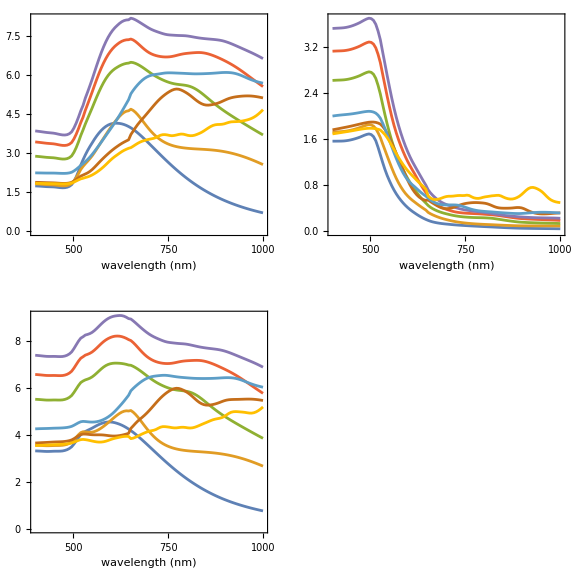

```mathematica
g2=Legended[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]]}},ImageSize->Large],Placed[LineLegend[Table[ColorData[97,i],{i,Length[dat]}],{"single sphere","bisphere","linear chain of 10 spheres","linear chain of 20 spheres","linear chain of 30 spheres","packed cluster of 10 spheres","packed cluster of 20 spheres","packed cluster of 30 spheres"},LabelStyle->{13,White}],{0.99,0.1}]]
```

top left to right: scattering cross section efficiency, absorption cross section efficiency
bottom left: extinction cross section efficiency

## Asymmetry parameter

```mathematica
vars={" length, ref index"};
len={1};
datRS1=readmstm["ref_sphere_var.dat",vars,len];
wav=(2 Pi)/datRS1[[All,1]] 0.1 ×1000;
apRS1=readap["ref_sphere_var.dat"];
apRS2=readap["ref_bisphere_var.dat"];
apLC10=readap["linear_chain_10_var.dat"];
apLC20=readap["linear_chain_20_var.dat"];
apLC30=readap["linear_chain_30_var.dat"];
apPC10=readap["packed_cluster_10_var.dat"];
apPC20=readap["packed_cluster_20_var.dat"];
apPC30=readap["packed_cluster_30_var.dat"];
ap={{wav,apRS1}ᵀ,{wav,apRS2}ᵀ,{wav,apLC10}ᵀ,{wav,apLC20}ᵀ,{wav,apLC30}ᵀ,{wav,apPC10}ᵀ,{wav,apPC20}ᵀ,{wav,apPC30}ᵀ};
```

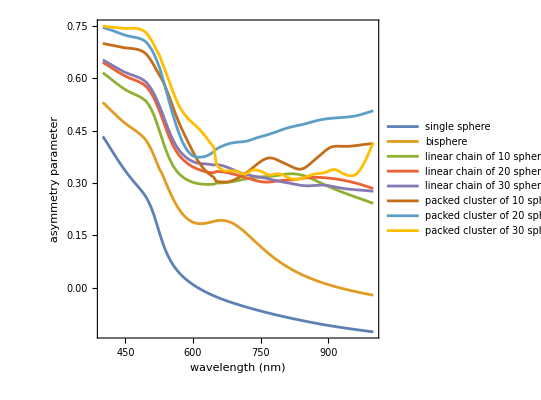

```mathematica
g=ListPlot[ap,PlotLegends->{"single sphere","bisphere","linear chain of 10 spheres","linear chain of 20 spheres","linear chain of 30 spheres","packed cluster of 10 spheres","packed cluster of 20 spheres","packed cluster of 30 spheres"}, Frame->True,Axes->False,FrameStyle->Medium,Joined->True,AspectRatio->1,FrameLabel->{"wavelength (nm)","asymmetry parameter"},PlotRangePadding->None]
```